```mathematica
data=Import[NotebookDirectory[]<>"corrected data.csv"];
```

```mathematica
dataCleaned=DeleteCases[data,x_/;x[[2]]<-0.001]
```

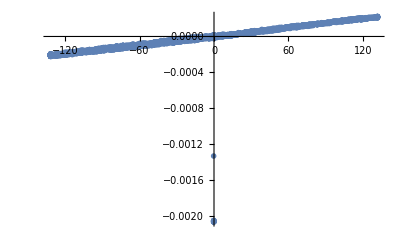

```mathematica
ListPlot[data,PlotStyle->PointSize[0.01],PlotRange->All]
```

```mathematica
fit=LinearModelFit[dataCleaned,x,x]
```

FittedModel[…]

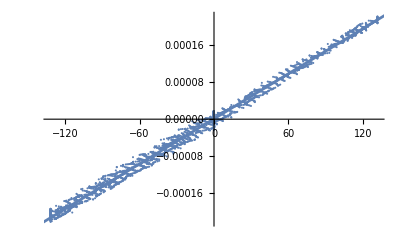

```mathematica
Show[ListPlot[dataCleaned],Plot[fit[x],{x,-200,200}]]
```

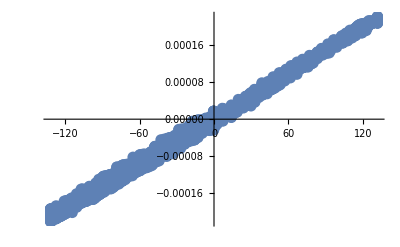

```mathematica
ListPlot[dataCleaned,PlotStyle->PointSize[0.02],PlotRange->All]
```

## Functions

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
f[{a_,b_}]:=TeXForm@NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//ToString//Quiet
```

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Regression

```mathematica
pars=ungewichteterReg[dataCleaned[[All,1]],dataCleaned[[All,2]]]
```

{8.64804×10^-7,1.62782×10^-6,1.57721×10^-7,1.97535×10^-9}

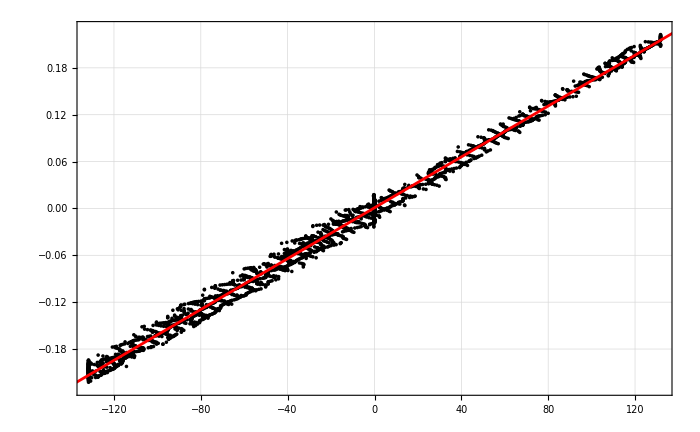

```mathematica
Show[ListPlot[{#[[1]],#[[2]]*10^3}&/@dataCleaned,pltsettings,PlotRange->{All,{-0.00023*10^3,0.00023*10^3}},PlotStyle->Black],Plot[10^3(pars[[1]]+pars[[2]]x),{x,-200,200},PlotStyle->Red]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/holzkern plot raw.pdf",Show[ListPlot[{#[[1]],#[[2]]*10^3}&/@dataCleaned,pltsettings,PlotRange->{All,{-0.00023*10^3,0.00023*10^3}},PlotStyle->Black],Plot[10^3(pars[[1]]+pars[[2]]x),{x,-200,200},PlotStyle->Red]],Background->None];
```

```mathematica
pars[[2]]/(4π*10^(-7))
pars[[4]]/(4π*10^(-7))
```

1.29538

0.00157194